## Setup

```mathematica
Get["FunKit`"]
```

Loading external dependencies...

TensorBases loaded

MaTeX loaded

Loading modules...

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

...DiRK loaded

...TRACY loaded

...COEN loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FInfo[].

```mathematica
fields= <|
"cField"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},
{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},
Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},
{cb,c},{cb,c,A}},
Field->{{}}
|>;
bases={
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",
{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",
{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
};
diagramStyling=<|
"Styles"->{A->{Red},c->{Black,Dashed},AnyField->{Black}}
|>;
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases(*,
"DiagramStyling"->diagramStyling*)
|>;

SetTexStyles[cb->"\\bar{c}"];
SetGlobalSetup[Setup];
landauGauge=(#/.dressing[GammaN,{A,A},2,{__}]:>1/ξ//.ξ->0)&;
dressingRules=Replace[#,{
dressing[GammaN,{A,A},2,{a_,b_}]:>1,
dressing[GammaN,{c,cb},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},1,{p1_,p2_}]:>Zc[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{c,cb,A},1,{p1_,p2_,p3_}]:>ZccbA[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

dressing[S,{c,cb,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[S,{c,cb},1,{p1_,p2_}]->sp[p2,p2],
dressing[S,{A,A},1,{p1_,p2_}]->sp[p2,p2],

ZccbA[p1_,p2_]:>ZccbA[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA3[p1_,p2_]:>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA4[p1_,p2_,p3_]:>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[-p1-p2-p3,-p1-p2-p3]))],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*((ZA[1.02evP]-ZA[evP])/(0.02*evP))),
dressing[Rdot,{c,cb},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k((Zc[1.02*k]-Zc[k])/(0.02*k)))
},Infinity]&;
SetSymmetricDressing[GammaN,{A,A}]
PropParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p1,p1]->p^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos1,√(a_^2):>a}//DiagramSimplify;
SPParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p,p]->p^2,sp[l1,l1]->l1^2,√(a_^2):>a}//DiagramSimplify;
SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1-1<cos2<1&&-1<cos3<1;
DefineFormExecutable["tform -w16"]
```

TFORM 4.3.1 (Apr 11 2023, v4.3.1) 64-bits

## DSE

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


2 -Graphics-+12 -Graphics--3 -Graphics--4 -Graphics---Graphics-+4 -Graphics-+4 -Graphics-+4 -Graphics-

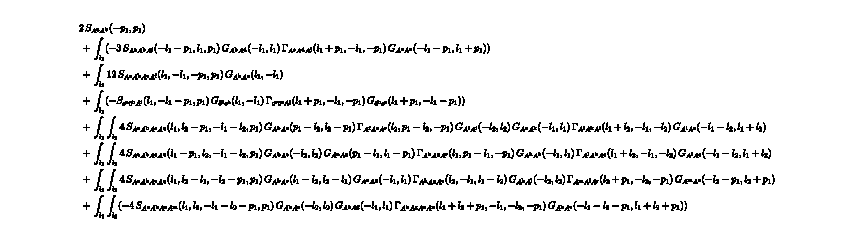

<|0-Loop→2 p^2,1-Loop→(12 (-1+cos1^2) gS (3 l1^4+6 cos1 l1^3 p+(8+cos1^2) l1^2 p^2+6 cos1 l1 p^3+3 p^4) ZA3[l1+p1,-l1])/(l1^2 (l1^2+2 cos1 l1 p+p^2)^2 Zc[l1] Zc[√(l1^2+2 cos1 l1 p+p^2)]),2-Loop→(72 gS^2 (sp[l1,l2]^3 (-5 p^2 sp[l2,l2]^2+(p^2-sp[l2,p1]) sp[l2,p1]^2+sp[l2,l2] (-8 p^4+12 p^2 sp[l2,p1]+sp[l2,p1]^2))+l1 sp[l1,l2] sp[l2,l2] (6 l1 (cos1 l1 p-2 sp[l2,p1]) (p^2-sp[l2,p1]) sp[l2,p1]+p sp[l2,l2]^2 (p (5 l1-2 cos1 p)+2 cos1 sp[l2,p1])+sp[l2,l2] (l1 p^3 (-4 cos1 l1+8 p+cos1^2 p)+p (-6 l1 p-cos1^2 l1 p+4 cos1 (l1^2+p^2)) sp[l2,p1]-(7 l1+4 cos1 p) sp[l2,p1]^2))+sp[l1,l2]^2 (-3 p^2 sp[l2,l2]^3+l1^2 (p^2-sp[l2,p1]) sp[l2,p1]^2+sp[l2,l2]^2 (-p^2 (5 l1^2+4 cos1 l1 p+5 p^2)+p (4 cos1 l1+7 p) sp[l2,p1]+sp[l2,p1]^2)+sp[l2,l2] (-8 l1^2 p^4+6 l1 p^2 (2 l1+cos1 p) sp[l2,p1]+(l1^2-6 cos1 l1 p+p^2) sp[l2,p1]^2-sp[l2,p1]^3))+l1^2 sp[l2,l2] (3 p^2 sp[l2,l2]^3+8 l1^2 sp[l2,p1]^2 (-p^2+sp[l2,p1])+sp[l2,l2]^2 (p^2 (5 l1^2-2 cos1 l1 p+5 p^2)+(2 cos1 l1-5 p) p sp[l2,p1]-3 sp[l2,p1]^2)+sp[l2,l2] ((8+cos1^2) l1^2 p^4-l1 p^2 ((8+cos1^2) l1-4 cos1 p) sp[l2,p1]-(5 l1^2+4 cos1 l1 p+5 p^2) sp[l2,p1]^2+5 sp[l2,p1]^3))) ZA3[l2,-l2+p1] ZA3[l1+l2,-l1])/(l1^4 p^2 sp[l2,l2]^2 (l1^2+2 sp[l1,l2]+sp[l2,l2])^2 (p^2+sp[l2,l2]-2 sp[l2,p1])^2 Zc[l1] Zc[√sp[l2,l2]] Zc[√(l1^2+2 sp[l1,l2]+sp[l2,l2])] Zc[√(p^2+sp[l2,l2]-2 sp[l2,p1])])|>

```mathematica
DSEAA=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
DSEAAResult=Map[
(FormTrace[
F[TBGetProjector["AA",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
]//dressingRules//FORMSimplify//PropParam)&,
DSEAA]
```

```mathematica
DSEcbc=TakeDerivatives[MakeDSE[Setup,c[i1]],{cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEcbcResult=Map[
(FormTrace[
F[TBGetProjector["cbc",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
]//dressingRules//FORMSimplify//PropParam)&,
DSEcbc]
```

-Graphics-+-Graphics-

-Graphics-

<|0-Loop→p^2,1-Loop→(3 (-1+cos1^2) gS p^2 ZccbA[l1+p1,-p1])/(l1^2 (l1^2+2 cos1 l1 p+p^2) ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[l1])|>

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[l1,p,p1,p2,p3];
```

```mathematica
DSEAcbc=TakeDerivatives[MakeDSE[Setup,c[i1]],{A[i3],cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEAcbcResult=Map[
(FormTrace[
F[TBGetProjector["Acbc",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEAcbc]
```

-Graphics---Graphics-+-Graphics-

-Graphics-

<|0-Loop→gS,1-Loop→(gS p (-2 (cos1-cos2+2 cos1^2 cos2-2 cos1 cos2^2) l1^3+2 (-3+cos1^2-2 cos1^3 cos2+6 cos2^2+cos1 cos2 (5+2 cos2^2)) l1^2 p+(-5 cos1-7 cos2+10 cos1^2 cos2+24 cos1 cos2^2+14 cos2^3) l1 p^2+3 (-1+2 cos1 cos2+2 cos2^2) p^3) ZA3[-p1-p2,l1+p1+p2] ZccbA[-l1-p2,p2])/(2 l1^2 (l1^2+2 cos2 l1 p+p^2) (l1^2+2 (cos1+cos2) l1 p+p^2)^2 ZA[√(l1^2+2 cos2 l1 p+p^2)] Zc[l1] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])|>

```mathematica
DSEA3=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i3],A[i2]},"Symmetries"->symmetryP3]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
DSEA3Result=Map[
(FormTrace[
F[TBGetProjector["AAAClassTrans",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"][[1]]/.MakeDiagrammaticRules[]//landauGauge]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEA3]
```

6 -Graphics--3 -Graphics--24 -Graphics-+6 -Graphics-+4 -Graphics-+8 -Graphics-+4 -Graphics-+8 -Graphics-+8 -Graphics-+4 -Graphics--2 -Graphics--8 -Graphics--16 -Graphics--8 -Graphics--8 -Graphics--8 -Graphics-

-Graphics-

<|0-Loop→6 gS,1-Loop→(2 gS (24 (2 cos1^3+3 cos1^2 cos2-3 cos1 cos2^2-2 cos2^3) l1^5+12 (6+8 cos1^4+28 cos1^3 cos2-11 cos2^2-16 cos2^4+2 cos1^2 (-1+6 cos2^2)-cos1 cos2 (11+32 cos2^2)) l1^4 p+2 (186+8 cos1^5 cos2-163 cos2^2-622 cos2^4-16 cos2^6+12 cos1^4 (10+3 cos2^2)+cos1^3 (404 cos2+40 cos2^3)-2 cos1^2 (14+109 cos2^2+10 cos2^4)-cos1 cos2 (163+1244 cos2^2+48 cos2^4)) l1^2 p^3-3 (-126+16 cos1^3 cos2+51 cos2^2+418 cos2^4+cos1^2 (-24+434 cos2^2)+cos1 cos2 (51+836 cos2^2)) p^5-(99 (-1+2 cos1 cos2+2 cos2^2) p^7)/l1^2+1/l1(cos1+2 cos2) p^2 (4 (36+4 cos1^4+50 cos1^3 cos2-97 cos2^2-26 cos2^4+cos1^2 (50+24 cos2^2)-cos1 cos2 (97+52 cos2^2)) l1^4+2 (241+88 cos1^3 cos2-480 cos2^2-112 cos2^4-8 cos1^2 (-8+3 cos2^2)-32 cos1 cos2 (15+7 cos2^2)) l1^2 p^2-231 (-1+2 cos1 cos2+2 cos2^2) p^4)) ZA3[-p1-p2,l1+p1+p2] ZA3[p2,l1])/(11 p (l1^2+2 cos2 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2 Zc[l1] Zc[√(l1^2+2 cos2 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]),2-Loop→-((12 gS^2 (24 (2 cos1^3+3 cos1^2 cos2-3 cos1 cos2^2-2 cos2^3) l1^9 p sp[l2,l2]+2 (-123+29 cos1^2+39 cos1 cos2+10 cos2^2) p^6 sp[l1,l2]^2 (sp[l1,l2]+sp[l2,l2])-2 l1 p^5 sp[l1,l2] (sp[l1,l2]+sp[l2,l2]) ((-479 cos1+85 cos1^3-289 cos2+112 cos1^2 cos2+5 cos1 cos2^2-22 cos2^3) sp[l1,l2]+(-206 cos1-15 cos2+28 cos1^2 cos2+64 cos1 cos2^2+36 cos2^3) sp[l2,p1]-(191 cos1+28 cos1^3-16 cos2+64 cos1^2 cos2+36 cos1 cos2^2) sp[l2,p2])-4 l1^8 (sp[l2,l2] ((44 cos1^4+90 cos1^3 cos2+cos1^2 (33-30 cos2^2)+cos1 (33 cos2-80 cos2^3)+6 (-3+cos2^2-4 cos2^4)) p^2+4 (2+2 cos1^2+3 cos1 cos2-cos2^2) sp[l2,p1]-8 (-2+cos1 cos2+cos2^2) sp[l2,p2])+4 sp[l1,l2] ((2+2 cos1^2+3 cos1 cos2-cos2^2) sp[l2,p1]-2 (-2+cos1 cos2+cos2^2) sp[l2,p2]))+4 l1^7 p ((-4 cos1^3-6 cos1^2 cos2+4 cos2 (4+cos2^2)+cos1 (8+6 cos2^2)) sp[l1,l2]^2+sp[l2,l2] (-62 cos1 p^2+163 cos1^3 p^2+40 cos1^5 p^2-28 cos2 p^2+242 cos1^2 cos2 p^2+104 cos1^4 cos2 p^2+cos1 cos2^2 p^2+10 cos1^3 cos2^2 p^2-46 cos2^3 p^2-100 cos1^2 cos2^3 p^2-50 cos1 cos2^4 p^2-4 cos2^5 p^2+10 (2 cos1^3+3 cos1^2 cos2-3 cos1 cos2^2-2 cos2^3) sp[l2,l2]+(32 cos1^3+26 cos2+68 cos1^2 cos2-8 cos2^3+8 cos1 (9+cos2^2)) sp[l2,p1]+112 cos1 sp[l2,p2]-4 cos1^3 sp[l2,p2]+36 cos2 sp[l2,p2]-32 cos1^2 cos2 sp[l2,p2]-48 cos1 cos2^2 sp[l2,p2]-16 cos2^3 sp[l2,p2])+2 sp[l1,l2] ((14 cos1^3+8 cos2+21 cos1^2 cos2-14 cos2^3+cos1 (4-21 cos2^2)) sp[l2,l2]+(16 cos1^3+13 cos2+34 cos1^2 cos2-4 cos2^3+4 cos1 (9+cos2^2)) sp[l2,p1]-2 (cos1^3+8 cos1^2 cos2+4 cos1 (-7+3 cos2^2)+cos2 (-9+4 cos2^2)) sp[l2,p2]))+l1^5 p (-8 (2 cos1^3+3 cos1^2 cos2-2 cos2 (8+cos2^2)-cos1 (8+3 cos2^2)) sp[l1,l2]^3-4 sp[l1,l2]^2 (-109 cos1 p^2-29 cos1^3 p^2+8 cos1^5 p^2-74 cos2 p^2-139 cos1^2 cos2 p^2+24 cos1^4 cos2 p^2-135 cos1 cos2^2 p^2+10 cos1^3 cos2^2 p^2-21 cos2^3 p^2-20 cos1^2 cos2^3 p^2-18 cos1 cos2^4 p^2-4 cos2^5 p^2+2 (2 cos1^3+3 cos1^2 cos2-2 cos2 (8+cos2^2)-cos1 (8+3 cos2^2)) sp[l2,l2]-4 (34 cos1+14 cos1^3+11 cos2+31 cos1^2 cos2+6 cos1 cos2^2-3 cos2^3) sp[l2,p1]-216 cos1 sp[l2,p2]+8 cos1^3 sp[l2,p2]-72 cos2 sp[l2,p2]+60 cos1^2 cos2 sp[l2,p2]+92 cos1 cos2^2 sp[l2,p2]+32 cos2^3 sp[l2,p2])+sp[l2,l2] (3 (-143 cos1+330 cos1^3-75 cos2+508 cos1^2 cos2+90 cos1 cos2^2-56 cos2^3) p^4+8 (32 cos1^5+84 cos1^4 cos2+cos1^3 (133+10 cos2^2)+cos1^2 (197 cos2-80 cos2^3)-2 cos2 (11+20 cos2^2+2 cos2^4)-2 cos1 (25+cos2^2+21 cos2^4)) p^2 sp[l2,l2]-4 (8 cos1^3+9 cos2+24 cos1^2 cos2+cos1 (29+8 cos2^2)) sp[l2,p1]^2-2 (32 cos1^5+56 cos1^4 cos2-4 cos1^2 cos2 (97+2 cos2^2)+6 cos1^3 (-67+4 cos2^2)+cos2 (-53+20 cos2^2)+cos1 (-391+50 cos2^2-8 cos2^4)) p^2 sp[l2,p2]-8 (cos1^2 cos2+2 cos2 (4+cos2^2)+cos1 (4+3 cos2^2)) sp[l2,p2]^2+2 sp[l2,p1] ((123 cos2+32 cos1^4 cos2-58 cos2^3-8 cos2^5+8 cos1^3 (40+7 cos2^2)+cos1^2 (274 cos2+24 cos2^3)+cos1 (393-152 cos2^2-8 cos2^4)) p^2+4 (-27 cos1+4 cos1^3-17 cos2+9 cos1^2 cos2+11 cos1 cos2^2+2 cos2^3) sp[l2,p2]))+2 sp[l1,l2] (-2 (8 cos1^3+9 cos2+24 cos1^2 cos2+cos1 (29+8 cos2^2)) sp[l2,p1]^2+sp[l2,p1] ((123 cos2+32 cos1^4 cos2-58 cos2^3-8 cos2^5+8 cos1^3 (40+7 cos2^2)+cos1^2 (274 cos2+24 cos2^3)+cos1 (393-152 cos2^2-8 cos2^4)) p^2+4 (-27 cos1+4 cos1^3-17 cos2+9 cos1^2 cos2+11 cos1 cos2^2+2 cos2^3) sp[l2,p2])+2 sp[l2,l2] ((96 cos1^5+2 cos2+248 cos1^4 cos2-105 cos2^3-8 cos2^5+cos1^3 (458+20 cos2^2)+cos1^2 (775 cos2-240 cos2^3)+cos1 (-53+132 cos2^2-116 cos2^4)) p^2+4 (14 cos1^3+11 cos2+31 cos1^2 cos2-3 cos2^3+cos1 (34+6 cos2^2)) sp[l2,p1]-4 (-54 cos1+2 cos1^3-18 cos2+15 cos1^2 cos2+23 cos1 cos2^2+8 cos2^3) sp[l2,p2])-sp[l2,p2] ((32 cos1^5+56 cos1^4 cos2-4 cos1^2 cos2 (97+2 cos2^2)+6 cos1^3 (-67+4 cos2^2)+cos2 (-53+20 cos2^2)+cos1 (-391+50 cos2^2-8 cos2^4)) p^2+4 (cos1^2 cos2+2 cos2 (4+cos2^2)+cos1 (4+3 cos2^2)) sp[l2,p2])))-l1^4 p^2 (4 (30-12 cos1^4-26 cos1^3 cos2+62 cos2^2+8 cos2^4+cos1^2 (85+6 cos2^2)+3 cos1 cos2 (71+8 cos2^2)) sp[l1,l2]^3-4 sp[l1,l2]^2 (-63 p^2-132 cos1^2 p^2+32 cos1^4 p^2-181 cos1 cos2 p^2+42 cos1^3 cos2 p^2-17 cos2^2 p^2-60 cos1^2 cos2^2 p^2-114 cos1 cos2^3 p^2-44 cos2^4 p^2+(12 cos1^4+26 cos1^3 cos2-cos1^2 (85+6 cos2^2)-3 cos1 cos2 (71+8 cos2^2)-2 (15+31 cos2^2+4 cos2^4)) sp[l2,l2]-2 (47+24 cos1^4+76 cos1^3 cos2-32 cos2^2-cos1 cos2 (-87+cos2^2)+cos1^2 (163+47 cos2^2)) sp[l2,p1]-92 sp[l2,p2]-462 cos1^2 sp[l2,p2]+24 cos1^4 sp[l2,p2]-252 cos1 cos2 sp[l2,p2]+74 cos1^3 cos2 sp[l2,p2]+82 cos2^2 sp[l2,p2]+118 cos1^2 cos2^2 sp[l2,p2]+68 cos1 cos2^3 sp[l2,p2]+8 cos2^4 sp[l2,p2])+sp[l2,l2] ((-147+310 cos1^2+310 cos1 cos2-32 cos2^2) p^4+4 (-105+308 cos1^4+608 cos1^3 cos2+21 cos2^2-100 cos2^4-8 cos1 cos2 (-17+37 cos2^2)+cos1^2 (113+80 cos2^2)) p^2 sp[l2,l2]-4 (19+16 cos1^3 cos2-25 cos2^2+4 cos2^4+4 cos1^2 (11+7 cos2^2)+cos1 cos2 (27+16 cos2^2)) sp[l2,p1]^2+2 (51+20 cos1^4+140 cos1^3 cos2-62 cos2^2+38 cos1 cos2 (3+2 cos2^2)+4 cos1^2 (107+49 cos2^2)) p^2 sp[l2,p2]-4 (-8+4 cos1^3 cos2+36 cos2^2+cos1 cos2 (67+4 cos2^2)+cos1^2 (33+8 cos2^2)) sp[l2,p2]^2+2 sp[l2,p1] ((63-20 cos1^3 cos2+16 cos2^2-76 cos2^4+cos1^2 (410-140 cos2^2)+cos1 (222 cos2-196 cos2^3)) p^2+2 (-22+16 cos1^4+28 cos1^3 cos2-7 cos2^2+4 cos2^4+4 cos1 cos2 (-22+3 cos2^2)+cos1^2 (-83+20 cos2^2)) sp[l2,p2]))+2 sp[l1,l2] (-2 (19+16 cos1^3 cos2-25 cos2^2+4 cos2^4+4 cos1^2 (11+7 cos2^2)+cos1 cos2 (27+16 cos2^2)) sp[l2,p1]^2+sp[l2,p2] ((51+20 cos1^4+140 cos1^3 cos2-62 cos2^2+38 cos1 cos2 (3+2 cos2^2)+4 cos1^2 (107+49 cos2^2)) p^2-2 (-8+4 cos1^3 cos2+36 cos2^2+cos1 cos2 (67+4 cos2^2)+cos1^2 (33+8 cos2^2)) sp[l2,p2])+sp[l2,p1] ((63-20 cos1^3 cos2+16 cos2^2-76 cos2^4+cos1^2 (410-140 cos2^2)+cos1 (222 cos2-196 cos2^3)) p^2+2 (-22+16 cos1^4+28 cos1^3 cos2-7 cos2^2+4 cos2^4+4 cos1 cos2 (-22+3 cos2^2)+cos1^2 (-83+20 cos2^2)) sp[l2,p2])+sp[l2,l2] ((936 cos1^4+1892 cos1^3 cos2+cos1^2 (619+396 cos2^2)+cos1 (786 cos2-700 cos2^3)-5 (42-19 cos2^2+44 cos2^4)) p^2+4 (47+24 cos1^4+76 cos1^3 cos2-32 cos2^2-cos1 cos2 (-87+cos2^2)+cos1^2 (163+47 cos2^2)) sp[l2,p1]-4 (-46+12 cos1^4+37 cos1^3 cos2+41 cos2^2+4 cos2^4+2 cos1 cos2 (-63+17 cos2^2)+cos1^2 (-231+59 cos2^2)) sp[l2,p2])))-2 l1^6 (2 sp[l1,l2]^2 ((18-12 cos1^4-26 cos1^3 cos2+30 cos2^2+8 cos2^4+cos1^2 (39+6 cos2^2)+3 cos1 cos2 (35+8 cos2^2)) p^2+8 (2+2 cos1^2+3 cos1 cos2-cos2^2) sp[l2,p1]-16 (-2+cos1 cos2+cos2^2) sp[l2,p2])+2 sp[l1,l2] (-2 (2+2 cos1^2+3 cos1 cos2-cos2^2) sp[l2,p1]^2-(-46+16 cos1^4+46 cos1^3 cos2+25 cos2^2+cos1 cos2 (-151+30 cos2^2)+cos1^2 (-258+68 cos2^2)) p^2 sp[l2,p2]+sp[l2,l2] ((-30+104 cos1^4+212 cos1^3 cos2+46 cos2^2-56 cos2^4+cos1^2 (127-72 cos2^2)+cos1 (193 cos2-188 cos2^3)) p^2+8 (2+2 cos1^2+3 cos1 cos2-cos2^2) sp[l2,p1]-16 (-2+cos1 cos2+cos2^2) sp[l2,p2])+sp[l2,p1] ((47+32 cos1^4+96 cos1^3 cos2-15 cos2^2-2 cos2^4-3 cos1 cos2 (-41+4 cos2^2)+2 cos1^2 (96+23 cos2^2)) p^2+4 (-2+cos1 cos2+cos2^2) sp[l2,p2]))+sp[l2,l2] (-4 (2+2 cos1^2+3 cos1 cos2-cos2^2) sp[l2,p1]^2+2 sp[l2,p1] ((47+32 cos1^4+96 cos1^3 cos2-15 cos2^2-2 cos2^4-3 cos1 cos2 (-41+4 cos2^2)+2 cos1^2 (96+23 cos2^2)) p^2+4 (-2+cos1 cos2+cos2^2) sp[l2,p2])+p^2 ((-126+384 cos1^4+760 cos1^3 cos2+19 cos2^2-108 cos2^4-8 cos1 cos2 (-19+42 cos2^2)+cos1^2 (129+116 cos2^2)) p^2+2 (72 cos1^4+148 cos1^3 cos2+cos1^2 (55-48 cos2^2)+cos1 (55 cos2-132 cos2^3)+10 (-3+cos2^2-4 cos2^4)) sp[l2,l2]-2 (-46+16 cos1^4+46 cos1^3 cos2+25 cos2^2+cos1 cos2 (-151+30 cos2^2)+cos1^2 (-258+68 cos2^2)) sp[l2,p2])))+l1^2 p^4 (4 (-105+32 cos1^4+42 cos1^3 cos2-40 cos2^2-44 cos2^4-3 cos1^2 (87+20 cos2^2)-2 cos1 cos2 (178+57 cos2^2)) sp[l1,l2]^3+sp[l1,l2]^2 (-147 p^2+58 cos1^2 p^2+78 cos1 cos2 p^2+20 cos2^2 p^2+4 (-105+32 cos1^4+42 cos1^3 cos2-40 cos2^2-44 cos2^4-3 cos1^2 (87+20 cos2^2)-2 cos1 cos2 (178+57 cos2^2)) sp[l2,l2]+2 (-126+20 cos1^3 cos2+19 cos2^2+76 cos2^4+2 cos1^2 (-319+70 cos2^2)+cos1 cos2 (-263+196 cos2^2)) sp[l2,p1]-204 sp[l2,p2]-1466 cos1^2 sp[l2,p2]-40 cos1^4 sp[l2,p2]-418 cos1 cos2 sp[l2,p2]-280 cos1^3 cos2 sp[l2,p2]+240 cos2^2 sp[l2,p2]-392 cos1^2 cos2^2 sp[l2,p2]-152 cos1 cos2^3 sp[l2,p2])+2 sp[l2,l2] (3 (41-86 cos1^2-86 cos1 cos2+8 cos2^2) p^2 sp[l2,l2]+(23-28 cos1 cos2-28 cos2^2) sp[l2,p1]^2+(13+28 cos1^2-8 cos1 cos2-36 cos2^2) sp[l2,p1] sp[l2,p2]+18 (-1+2 cos1^2+2 cos1 cos2) sp[l2,p2]^2)+2 sp[l1,l2] ((23-28 cos1 cos2-28 cos2^2) sp[l2,p1]^2+(13+28 cos1^2-8 cos1 cos2-36 cos2^2) sp[l2,p1] sp[l2,p2]+18 (-1+2 cos1^2+2 cos1 cos2) sp[l2,p2]^2+sp[l2,l2] ((123-384 cos1^2-374 cos1 cos2+50 cos2^2) p^2+(-126+20 cos1^3 cos2+19 cos2^2+76 cos2^4+2 cos1^2 (-319+70 cos2^2)+cos1 cos2 (-263+196 cos2^2)) sp[l2,p1]-(102+20 cos1^4+140 cos1^3 cos2-120 cos2^2+19 cos1 cos2 (11+4 cos2^2)+cos1^2 (733+196 cos2^2)) sp[l2,p2])))+l1^3 p^3 (4 (-8 cos1^5-24 cos1^4 cos2+cos1^3 (89-10 cos2^2)+5 cos1^2 cos2 (61+4 cos2^2)+2 cos2 (68+7 cos2^2+2 cos2^4)+2 cos1 (97+117 cos2^2+9 cos2^4)) sp[l1,l2]^3+sp[l1,l2]^2 (555 cos1 p^2-170 cos1^3 p^2+327 cos2 p^2-224 cos1^2 cos2 p^2-10 cos1 cos2^2 p^2+44 cos2^3 p^2+4 (-8 cos1^5-24 cos1^4 cos2+cos1^3 (89-10 cos2^2)+5 cos1^2 cos2 (61+4 cos2^2)+2 cos2 (68+7 cos2^2+2 cos2^4)+2 cos1 (97+117 cos2^2+9 cos2^4)) sp[l2,l2]+4 (101 cos2+16 cos1^4 cos2-65 cos2^3-4 cos2^5+4 cos1^3 (58+7 cos2^2)+cos1^2 cos2 (137+12 cos2^2)+cos1 (355-190 cos2^2-4 cos2^4)) sp[l2,p1]+1476 cos1 sp[l2,p2]+1276 cos1^3 sp[l2,p2]-64 cos1^5 sp[l2,p2]+276 cos2 sp[l2,p2]+936 cos1^2 cos2 sp[l2,p2]-112 cos1^4 cos2 sp[l2,p2]-764 cos1 cos2^2 sp[l2,p2]-48 cos1^3 cos2^2 sp[l2,p2]-368 cos2^3 sp[l2,p2]+16 cos1^2 cos2^3 sp[l2,p2]+16 cos1 cos2^4 sp[l2,p2])+2 sp[l2,l2] ((-353 cos1+814 cos1^3-187 cos2+1260 cos1^2 cos2+230 cos1 cos2^2-144 cos2^3) p^2 sp[l2,l2]+(-91 cos1-29 cos2+20 cos1^2 cos2+72 cos1 cos2^2+52 cos2^3) sp[l2,p1]^2+2 sp[l2,p2] ((51 cos1+14 cos1^3-13 cos2+32 cos1^2 cos2+18 cos1 cos2^2) p^2+(8 cos1-34 cos1^3+cos2-72 cos1^2 cos2-38 cos1 cos2^2) sp[l2,p2])-sp[l2,p1] (2 (-63 cos1-7 cos2+14 cos1^2 cos2+32 cos1 cos2^2+18 cos2^3) p^2+(123 cos1+20 cos1^3+51 cos2+4 cos1^2 cos2-92 cos1 cos2^2-76 cos2^3) sp[l2,p2]))-2 sp[l1,l2] ((29 cos2-20 cos1^2 cos2-52 cos2^3+cos1 (91-72 cos2^2)) sp[l2,p1]^2+sp[l2,p1] (2 (-63 cos1-7 cos2+14 cos1^2 cos2+32 cos1 cos2^2+18 cos2^3) p^2+(20 cos1^3+51 cos2+4 cos1^2 cos2-76 cos2^3+cos1 (123-92 cos2^2)) sp[l2,p2])+2 sp[l2,p2] (-((14 cos1^3-13 cos2+32 cos1^2 cos2+3 cos1 (17+6 cos2^2)) p^2)+(34 cos1^3-cos2+72 cos1^2 cos2+cos1 (-8+38 cos2^2)) sp[l2,p2])+2 sp[l2,l2] ((145 cos1-612 cos1^3+68 cos2-955 cos1^2 cos2-180 cos1 cos2^2+103 cos2^3) p^2-(101 cos2+16 cos1^4 cos2-65 cos2^3-4 cos2^5+4 cos1^3 (58+7 cos2^2)+cos1^2 cos2 (137+12 cos2^2)+cos1 (355-190 cos2^2-4 cos2^4)) sp[l2,p1]+(16 cos1^5+28 cos1^4 cos2-2 cos1^2 cos2 (117+2 cos2^2)+23 cos2 (-3+4 cos2^2)+cos1^3 (-319+12 cos2^2)+cos1 (-369+191 cos2^2-4 cos2^4)) sp[l2,p2])))) ZA3[l1+l2,-l2] ZA3[-p1-p2,l1] ZA3[p2,l1-p1-p2])/(11 l1^2 p^2 (l1^2-2 cos1 l1 p+p^2)^2 (l1^2-2 (cos1+cos2) l1 p+p^2)^2 sp[l2,l2]^2 (l1^2+2 sp[l1,l2]+sp[l2,l2])^2 Zc[l1] Zc[√(l1^2-2 cos1 l1 p+p^2)] Zc[√(l1^2-2 (cos1+cos2) l1 p+p^2)] Zc[√sp[l2,l2]] Zc[√(l1^2+2 sp[l1,l2]+sp[l2,l2])]))|>

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
DSEA4=TakeDerivatives[MakeDSE[Setup,A[i1]],{A[i4],A[i3],A[i2]},"Symmetries"->symmetryP4]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
```

24 -Graphics--36 -Graphics-+9 -Graphics-+9 -Graphics-+72 -Graphics-+12 -Graphics-+12 -Graphics-+12 -Graphics--18 -Graphics--12 -Graphics--12 -Graphics--24 -Graphics--12 -Graphics--12 -Graphics--12 -Graphics--24 -Graphics--24 -Graphics--12 -Graphics--12 -Graphics--12 -Graphics--24 -Graphics--12 -Graphics--24 -Graphics--12 -Graphics--24 -Graphics--12 -Graphics--12 -Graphics--6 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-+24 -Graphics-

-Graphics-

## fRG

```mathematica
TakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FTex
```

\begin{aligned}  &(-G^{\bar{c}^{\text{a}}c^{\text{b}}}\,\Gamma_{c^{\text{b}}\bar{c}^{\text{c}}A^{i_2}}\,G^{\bar{c}^{\text{c}}c^{\text{d}}}\,\Gamma_{c^{\text{d}}\bar{c}^{\text{e}}A^{i_1}}\,G^{\bar{c}^{\text{e}}c^{\text{f}}}\,\partial_t R_{c^{\text{f}}\bar{c}^{\text{a}}})
    \\ &\,+\,(-G^{\bar{c}^{\text{a}}c^{\text{b}}}\,\Gamma_{c^{\text{c}}\bar{c}^{\text{a}}A^{i_2}}\,G^{\bar{c}^{\text{d}}c^{\text{c}}}\,\Gamma_{c^{\text{e}}\bar{c}^{\text{d}}A^{i_1}}\,G^{\bar{c}^{\text{f}}c^{\text{e}}}\,\partial_t R_{c^{\text{b}}\bar{c}^{\text{f}}})
    \\ &\,+\,G^{A^{\text{a}}A^{\text{b}}}\,\Gamma_{A^{i_2}A^{\text{c}}A^{\text{a}}}\,G^{A^{\text{d}}A^{\text{c}}}\,\Gamma_{A^{\text{e}}A^{\text{d}}A^{i_1}}\,G^{A^{\text{f}}A^{\text{e}}}\,\partial_t R_{A^{\text{f}}A^{\text{b}}}
    \\ &\,+\,(-\frac{1}{2}\,G^{A^{\text{a}}A^{\text{b}}}\,\Gamma_{A^{i_2}A^{\text{c}}A^{\text{a}}A^{i_1}}\,G^{A^{\text{d}}A^{\text{c}}}\,\partial_t R_{A^{\text{d}}A^{\text{b}}})
\end{aligned}

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


--Graphics-/2-2 -Graphics-+-Graphics-

-Graphics-

((7-cos1^2) (-RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] (-dtZA[(1+k^6)^(1/6)]+(50 k^6 (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)]))/(1+k^6))) ZA4[(√(l1^2+p^2))/(√2)])/(l1^4 Zc[l1]^2)+(2 (6 l1^4 (l1^2-2 cos1 l1 p+p^2) ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2+12 cos1 l1 p (l1^2+p^2) (l1^2-2 cos1 l1 p+p^2) ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2+2 p^2 (l1^2-2 cos1 l1 p+p^2) (8 l1^2+3 p^2) ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2+(1+k^6) l1^2 (l1^2+2 cos1 l1 p+p^2)^2 (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)]^2-cos1^2 (6 l1^4 (l1^2-2 cos1 l1 p+p^2) ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2+2 p^2 (l1^2-2 cos1 l1 p+p^2) (7 l1^2+3 p^2) ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2+2 cos1 l1 p (l1^2-2 cos1 l1 p+p^2) (6 l1^2+cos1 l1 p+6 p^2) ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2+(1+k^6) l1^2 (l1^2+2 cos1 l1 p+p^2)^2 (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)]^2)))/((1+k^6) l1^4 (l1^2-2 cos1 l1 p+p^2) (l1^2+2 cos1 l1 p+p^2)^2 ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])

```mathematica
fRGAA=TakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
traceExprAA=F[TBGetProjector["AA",1,{i1,i2}/.fRGAA[[1]]["externalIndices"]],(fRGAA[[1]]["result"]/.MakeDiagrammaticRules[]//landauGauge)];
FlowAA=FormTrace[traceExprAA]//.dressingRules//FORMSimplify//PropParam
```

```mathematica
fRGcbc=TakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
traceExprcbc=F[TBGetProjector["cbc",1,{i1,i2}/.fRGcbc[[1]]["externalIndices"]],(fRGcbc[[1]]["result"]/.MakeDiagrammaticRules[]//landauGauge)];
Flowcbc=FormTrace[traceExprcbc]//.dressingRules//FORMSimplify//PropParam
```

--Graphics---Graphics-

-Graphics-

-((3 (-1+cos1^2) p^2 ((1+k^6) RBdot[k^2,l1^2] (-l1^2 ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[k] Zc[l1]^2+(l1^2+2 cos1 l1 p+p^2) ZA[(1+k^6)^(1/6)] ZA[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])-RB[k^2,l1^2] ((1+k^6) l1^2 ZA[√(l1^2+2 cos1 l1 p+p^2)] (dtZc[k]+50 (-Zc[k]+Zc[(51 k)/50])) Zc[l1]^2-(l1^2+2 cos1 l1 p+p^2) ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)])) ZA[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])) ZccbA[√(2/3) √(l1^2+cos1 l1 p+p^2)]^2)/((1+k^6) l1^4 (l1^2+2 cos1 l1 p+p^2)^2 ZA[l1]^2 ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)]))

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[l1,p,p1,p2,p3];
```

```mathematica
fRGAcbc=TakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
projectorAcbc=TBGetProjector["Acbc",1,{i1,i2,i3}/.fRGAcbc[[1]]["externalIndices"]];
traceExprAcbc=F[projectorAcbc,(fRGAcbc[[1]]["result"]/.MakeDiagrammaticRules[]//landauGauge)];FlowAcbc=FormTrace[traceExprAcbc,SP3FormRule,SP3FormRule]//.dressingRules//FORMSimplify[#,SP3FormRule,SP3FormRule]&//SPParam
```

--Graphics-/2--Graphics-/2+-Graphics-/2+-Graphics-/2+-Graphics---Graphics---Graphics-/2--Graphics-/2+-Graphics-/2+-Graphics-/2

-Graphics-

1/(4 l1^4 (l1^2-2 cos1 l1 p+p^2)^2 (l1^2+2 cos2 l1 p+p^2)^2)p (((l1^2+2 cos2 l1 p+p^2) (2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2)-2 (-3+2 cos1^3 cos2+2 cos2^2+cos1 cos2 (-3+4 cos2^2)+cos1^2 (1+6 cos2^2)) l1^2 p+(2 cos2-10 cos1^2 cos2+cos1 (-5+4 cos2^2)) l1 p^2+3 (1+2 cos1 cos2) (p^2)^(3/2)) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2-cos1 l1 p+p^2)])/((1+k^6) ZA[√(l1^2+2 cos2 l1 p+p^2)] Zc[l1]^2 Zc[√(l1^2-2 cos1 l1 p+p^2)])+(2 (cos1+2 cos2) l1^2 ((-1+2 cos1 cos2+2 cos2^2) l1+(2 cos1+cos2) p) (l1^2-2 cos1 l1 p+p^2) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)])/(ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] Zc[√(l1^2+2 cos2 l1 p+p^2)])) ZccbA[√(2/3) √(l1^2+cos2 l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (-cos1+cos2) l1 p+p^2)]+(p ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] (1/((1+k^6) (l1^2-2 cos2 l1 p+p^2) ZA[√(l1^2-2 cos2 l1 p+p^2)])(-2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2)-2 (-3+2 cos1^3 cos2+2 cos2^2+cos1 cos2 (-3+4 cos2^2)+cos1^2 (1+6 cos2^2)) l1^2 p+(-2 cos2+10 cos1^2 cos2+cos1 (5-4 cos2^2)) l1 p^2+3 (1+2 cos1 cos2) (p^2)^(3/2)) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZccbA[√((2 l1^2)/3+2/3 (cos1-cos2) l1 p+p^2)] ZccbA[√(2/3) √(l1^2-cos2 l1 p+p^2)]+1/((l1^2+2 (cos1+cos2) l1 p+p^2) ZA[√(l1^2+2 (cos1+cos2) l1 p+p^2)]^2)(1/(1+k^6)(2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2)+2 (3+2 cos1^3 cos2-2 cos2^2+6 cos1^2 (-1+cos2^2)+cos1 cos2 (-7+4 cos2^2)) l1^2 p+(-14 cos1^3+2 cos2-18 cos1^2 cos2+cos1 (7-4 cos2^2)) l1 p^2-3 (-1+2 cos1^2+2 cos1 cos2) (p^2)^(3/2)) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA[√(l1^2+2 (cos1+cos2) l1 p+p^2)]+1/(l1^2+2 (cos1+cos2) l1 p+p^2)2 l1^2 (-2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2)-2 (3+2 cos1^3 cos2-2 cos2^2+6 cos1^2 (-1+cos2^2)+cos1 cos2 (-7+4 cos2^2)) l1^2 p+(14 cos1^3-2 cos2+18 cos1^2 cos2+cos1 (-7+4 cos2^2)) l1 p^2+3 (-1+2 cos1^2+2 cos1 cos2) (p^2)^(3/2)) (dtZc[k] RB[k^2,l1^2+2 (cos1+cos2) l1 p+p^2]+RBdot[k^2,l1^2+2 (cos1+cos2) l1 p+p^2] Zc[k]-50 RB[k^2,l1^2+2 (cos1+cos2) l1 p+p^2] (Zc[k]-Zc[(51 k)/50])) Zc[l1]) ZccbA[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]))/(4 l1^4 (l1^2+2 cos1 l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)])+(p ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] (1/((l1^2-2 cos1 l1 p+p^2)^2 Zc[√(l1^2-2 cos1 l1 p+p^2)])(-2 (-2 cos2+2 cos1^2 cos2+4 cos2^3+cos1 (-1+6 cos2^2)) (l1^2)^(3/2)+2 (3+2 cos1^3 cos2-2 cos2^2+6 cos1^2 (-1+cos2^2)+cos1 cos2 (-7+4 cos2^2)) l1^2 p+(14 cos1^3-2 cos2+18 cos1^2 cos2+cos1 (-7+4 cos2^2)) l1 p^2-3 (-1+2 cos1^2+2 cos1 cos2) (p^2)^(3/2)) ZA3[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (2 cos1+cos2) l1 p+p^2)]-((-1+2 cos1 cos2+2 cos2^2) (2 cos1 l1+4 cos2 l1-3 p) ZccbA[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (cos1+2 cos2) l1 p+p^2)])/((l1^2-2 cos2 l1 p+p^2) ZA[√(l1^2-2 cos2 l1 p+p^2)])))/(4 (1+k^6) l1^4 (l1^2-2 (cos1+cos2) l1 p+p^2) ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)] Zc[l1]^2)+1/(8 l1^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2)p ZccbA[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ((2 (cos1+2 cos2) ((-1+2 cos1 cos2+2 cos2^2) l1+(-cos1+cos2) p) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)])/((l1^2+2 cos1 l1 p+p^2) ZA[l1]^2 ZA[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])-((-1+2 cos1 cos2+2 cos2^2) (2 cos1 l1+4 cos2 l1+3 p) (dtZc[k] RB[k^2,l1^2+2 (cos1+cos2) l1 p+p^2]+RBdot[k^2,l1^2+2 (cos1+cos2) l1 p+p^2] Zc[k]-50 RB[k^2,l1^2+2 (cos1+cos2) l1 p+p^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2+cos2 l1 p+p^2)] ZccbA[√((2 l1^2)/3+2/3 (cos1+2 cos2) l1 p+p^2)])/((l1^2+2 cos2 l1 p+p^2) ZA[√(l1^2+2 cos2 l1 p+p^2)] ZA[√(l1^2+2 (cos1+cos2) l1 p+p^2)]^2 Zc[l1]))

```mathematica
fRGA3=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
projectorA3=TBGetProjector["AAAClassTrans",1,{i1,i2,i3}/.fRGA3[[1]]["externalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//Simplify;
traceExprA3=F[projectorA3,(fRGA3[[1]]["result"]/.MakeDiagrammaticRules[]//landauGauge)];
FlowA3=FormTrace[traceExprA3,{},SP3FormRule]//.dressingRules//FORMSimplify[#,{},SP3FormRule]&//SPParam
```

(3 -Graphics-)/2+(3 -Graphics-)/2-6 -Graphics--3 -Graphics-

-Graphics-

-(9 (-1+cos2^2) p^2 ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZA4[1/2 √(2 l1^2-2 cos2 l1 p+3 p^2)])/(2 (1+k^6) l1^4 (l1^2-2 cos2 l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2-2 cos2 l1 p+p^2)])-(3 p ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) (l1^4 (cos2 (54+4 cos1^2+4 cos1 cos2-53 cos2^2) ZA3[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZA4[1/2 √(2 l1^2-2 cos2 l1 p+3 p^2)] Zc[√(l1^2+2 cos1 l1 p+p^2)]+cos1 (-54+53 cos1^2-4 cos1 cos2-4 cos2^2) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2-2 cos2 l1 p+p^2)])+p^4 (cos2 (54+4 cos1^2+4 cos1 cos2-53 cos2^2) ZA3[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZA4[1/2 √(2 l1^2-2 cos2 l1 p+3 p^2)] Zc[√(l1^2+2 cos1 l1 p+p^2)]+cos1 (-54+53 cos1^2-4 cos1 cos2-4 cos2^2) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2-2 cos2 l1 p+p^2)])-2 l1^2 p^2 (-((1+2 cos1^2) cos2 (54+4 cos1^2+4 cos1 cos2-53 cos2^2) ZA3[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZA4[1/2 √(2 l1^2-2 cos2 l1 p+3 p^2)] Zc[√(l1^2+2 cos1 l1 p+p^2)])-cos1 (-54+53 cos1^2-4 cos1 cos2-4 cos2^2) (1+2 cos2^2) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2-2 cos2 l1 p+p^2)])+4 cos1 cos2 (l1^2)^(3/2) p ((54+4 cos1^2+4 cos1 cos2-53 cos2^2) ZA3[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZA4[1/2 √(2 l1^2-2 cos2 l1 p+3 p^2)] Zc[√(l1^2+2 cos1 l1 p+p^2)]+(54-53 cos1^2+4 cos1 cos2+4 cos2^2) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2-2 cos2 l1 p+p^2)])+4 cos1 cos2 l1 (p^2)^(3/2) ((54+4 cos1^2+4 cos1 cos2-53 cos2^2) ZA3[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZA4[1/2 √(2 l1^2-2 cos2 l1 p+3 p^2)] Zc[√(l1^2+2 cos1 l1 p+p^2)]+(54-53 cos1^2+4 cos1 cos2+4 cos2^2) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2-2 cos2 l1 p+p^2)])))/(22 (1+k^6) (l1^2)^(3/2) (l1^2+2 cos1 l1 p+p^2)^2 (l1^2-2 cos2 l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2-2 cos2 l1 p+p^2)])+(12 (-6+16 cos1^4+32 cos1^3 cos2+2 cos2^2-8 cos2^4+cos1^2 (11-12 cos2^2)+cos1 (11 cos2-28 cos2^3)) l1^2 ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)])/(11 (1+k^6) (l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])+(((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] (48 (2 cos1^3+3 cos1^2 cos2-3 cos1 cos2^2-2 cos2^3) (l1^2)^(7/2) ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]+8 (52 cos1^5+130 cos1^4 cos2+2 cos1^3 (97+2 cos2^2)+cos1^2 (291 cos2-124 cos2^3)-2 cos2 (18+25 cos2^2+2 cos2^4)-cos1 (72+3 cos2^2+58 cos2^4)) (l1^2)^(5/2) p^2 ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]-396 (-1+cos1^2) (cos1+cos2) l1 p^6 ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]-99 (-1+cos1^2) l1^4 (p^2)^(3/2) ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]-198 (-1+cos1^2) (1+2 cos1^2+4 cos1 cos2+2 cos2^2) l1^2 (p^2)^(5/2) ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]+99 (p^2)^(7/2) (2 (-1+2 cos1^2+2 cos1 cos2) ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]-(-1+cos1^2) ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])+4 (l1^2)^(3/2) p^4 ((224 cos1^5+560 cos1^4 cos2+16 cos1^3 (60+17 cos2^2)-8 cos1^2 cos2 (-180+19 cos2^2)-cos2 (241+64 cos2^2)+cos1 (-482+352 cos2^2-88 cos2^4)) ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]-99 (-1+cos1^2) (cos1+cos2) ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])))/(22 (1+k^6) l1^4 √(p^2) (l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])+1/(22 (1+k^6) l1^2 Zc[l1]^2)(1/((l1^2-2 cos2 l1 p+p^2)^2 Zc[√(l1^2-2 cos2 l1 p+p^2)])3 (54+4 cos1^2+4 cos1 cos2-53 cos2^2) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2-cos2 l1 p+p^2)] ZA4[1/2 √(2 l1^2-2 cos2 l1 p+3 p^2)]+(4 (16 cos1^6+48 cos1^5 cos2+cos1^4 (622+20 cos2^2)+cos1^3 (1244 cos2-40 cos2^3)+cos1^2 (163+218 cos2^2-36 cos2^4)-2 (93-14 cos2^2+60 cos2^4)+cos1 (163 cos2-404 cos2^3-8 cos2^5)) l1^2 p^2 ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)])/((l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])-(3 ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] (-2 (418 cos1^4+836 cos1^3 cos2-6 (21+4 cos2^2)+cos1 cos2 (51+16 cos2^2)+cos1^2 (51+434 cos2^2)) p^4 ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)]+(-54+53 cos1^2-4 cos1 cos2-4 cos2^2) (l1^2+2 (cos1+cos2) l1 p+p^2)^2 ((1+k^6) (dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)])-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA4[1/2 √(2 l1^2+2 cos1 l1 p+3 p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]))/((l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)]))-(cos1 (cos1+cos2) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (2 cos1+cos2) l1 p+p^2)])/(l1^2 (l1^2-2 cos1 l1 p+p^2) (l1^2-2 (cos1+cos2) l1 p+p^2) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)])-(2 (-3+cos2^2) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (2 cos1+cos2) l1 p+p^2)])/(11 l1^2 (l1^2-2 cos1 l1 p+p^2) (l1^2-2 (cos1+cos2) l1 p+p^2) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)])+1/(11 (l1^2)^(3/2) √(p^2))((231 (4 cos1^3-cos2+6 cos1^2 cos2+2 cos1 (-1+cos2^2)) p^6 ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA3[√(2/3) √(l1^2+(cos1+cos2) l1 p+p^2)] ZA3[√((2 l1^2)/3+2/3 (2 cos1+cos2) l1 p+p^2)])/((1+k^6) (l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2) l1 p+p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+p^2)])+(2 (2 cos1^3+3 cos1^2 cos2-3 cos1 cos2^2-2 cos2^3) l1^2 (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2) l1 p+p^2)] ZccbA[√((2 l1^2)/3-2/3 (2 cos1+cos2) l1 p+p^2)])/((l1^2-2 cos1 l1 p+p^2) (l1^2-2 (cos1+cos2) l1 p+p^2) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+p^2)]))

## 4Point

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
SP4FormRule=MakeSPFormRule[l1,p,p1,p2,p3,p4];
```

```mathematica
fRGA4=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3],A[i4]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
projectorA4=TBGetProjector["AAAAClassTrans",1,{i1,i2,i3,i4}/.fRGA4[[1]]["externalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&//Simplify;
traceExprA4=F[projectorA4,(fRGA4[[1]]["result"]/.MakeDiagrammaticRules[]//landauGauge)];
FlowA4=FormTrace[traceExprA4,SP4FormRule,SP4FormRule]//.dressingRules//FORMSimplify[#,SP4FormRule,SP4FormRule]&//SPParam
```

3 -Graphics--6 -Graphics--6 -Graphics--6 -Graphics--24 -Graphics-+12 -Graphics-

-Graphics-

-((3 ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA3[1/3 √(6 l1^2+6 (2 cos1+cos2) l1 p+10 p^2)] (8/3 (81 (-72 cos2^5-180 cos2^4 cos3+cos2^3 (6-108 cos3^2)+3 cos2^2 cos3 (5+6 cos3^2)+2 cos3 (-2+9 cos3^4)+cos2 (4-3 cos3^2+54 cos3^4)+cos1 (53 cos2^2-252 cos2^4+cos3 (-408 cos2^3+cos3 (-47-54 cos2^2+12 cos3 (16 cos2+9 cos3)))+cos1 (41 cos2-252 cos2^3+cos3 (-59-138 cos2^2+6 cos3 (32 cos2+33 cos3))+6 cos1 (-1-3 cos2^2+9 cos3 (4 cos2+3 cos3)+3 cos1 (3 cos1+5 (cos2+2 cos3)))))) (l1^2)^(9/2) p-9 (2 cos2 (88+258 cos2^2+1161 cos2^4+54 cos2^6)-cos3 (-112-378 cos2^6-432 cos2^5 cos3+6 cos3^2+414 cos3^4-45 cos2^4 (125+3 cos3^2)+18 cos2^3 cos3 (-169+6 cos3^2)+3 cos2 cos3 (-166+546 cos3^2+9 cos3^4)+9 cos2^2 (-106+129 cos3^2+12 cos3^4))-3 cos1 (-96+252 cos1^6-594 cos2^6-1752 cos2^5 cos3-152 cos3^2+874 cos3^4+27 cos3^6+9 cos1^5 (83 cos2+113 cos3)-6 cos2^3 cos3 (759+8 cos3^2)-7 cos2^4 (391+213 cos3^2)+6 cos1^4 (133+84 cos2^2+406 cos2 cos3+219 cos3^2)+cos1^3 (2264 cos2-1224 cos2^3+1726 cos3+804 cos2^2 cos3+2691 cos2 cos3^2+1359 cos3^3)+6 cos2 cos3 (32+273 cos3^2+54 cos3^4)+cos2^2 (318-873 cos3^2+600 cos3^4)+cos1^2 (506-2727 cos2^4-3456 cos2^3 cos3+467 cos3^2+1089 cos3^4+12 cos2 cos3 (237+232 cos3^2)+cos2^2 (1543+738 cos3^2))+cos1 (-2052 cos2^5-4449 cos2^4 cos3-8 cos2^3 (253+255 cos3^2)+3 cos2^2 cos3 (-411+482 cos3^2)+cos3 (524+1049 cos3^2+342 cos3^4)+cos2 (994+810 cos3^2+1629 cos3^4)))) (l1^2)^(7/2) (p^2)^(3/2)+3 (-2 cos2 (2224+2421 cos2^2+3321 cos2^4)+cos3 (-1208-9 cos2^2 (656+1847 cos2^2)-51 cos2 (10+219 cos2^2) cos3+6 cos3^2 (67+78 cos2^2+6 cos3 (74 cos2+19 cos3)))+cos1 (-5656+1728 cos1^6-1728 cos2^6-5184 cos2^5 cos3+7804 cos3^2+3918 cos3^4+54 cos3^6+18 cos1^5 (409 cos2+263 cos3)+12 cos2^3 cos3 (-4139+45 cos3^2)+6 cos1^4 (3548+1761 cos2^2+2499 cos2 cos3+447 cos3^2)-3 cos2^4 (9091+1377 cos3^2)+6 cos2 cos3 (2636+808 cos3^2+99 cos3^4)+cos2^2 (1106-20079 cos3^2+1755 cos3^4)+3 cos1^2 (5930-2784 cos2^4-3882 cos2^3 cos3+5097 cos3^2+708 cos3^4+cos2^2 (15661+42 cos3^2)+2 cos2 cos3 (13202+771 cos3^2))+3 cos1^3 (702 cos2^3+3507 cos2^2 cos3+3 cos3 (5033+86 cos3^2)+cos2 (20381+2283 cos3^2))+cos1 (-7254 cos2^5-17037 cos2^4 cos3+36 cos2^2 cos3 (59+111 cos3^2)-3 cos2^3 (4729+2886 cos3^2)+2 cos3 (15017+579 cos3^2+540 cos3^4)+cos2 (23336+9603 cos3^2+4275 cos3^4)))) (l1^2)^(5/2) (p^2)^(5/2)+2 (25038 cos1^5+9 cos1^4 (8431 cos2+5479 cos3)+3 cos1^3 (8854+25497 cos2^2+33738 cos2 cos3+7785 cos3^2)-2 (3120 cos2^3+928 cos3+2706 cos2^2 cos3-312 cos3^3+cos2 (4357-591 cos3^2))+cos1^2 (25929 cos2^3+47060 cos3+53433 cos2^2 cos3-1350 cos3^3+cos2 (32626+24408 cos3^2))+cos1 (279 cos2^4+1962 cos2^3 cos3-6 cos2 cos3 (-4658+201 cos3^2)+cos2^2 (448+909 cos3^2)-2 (5285-7441 cos3^2+216 cos3^4))) (l1^2)^(3/2) (p^2)^(7/2)+4 (5139 cos1^3-1504 cos2-209 cos3+cos1^2 (8547 cos2+6870 cos3)+3 cos1 (-571+1136 cos2^2+1713 cos2 cos3+577 cos3^2)) l1 (p^2)^(9/2)+p^6 ((21960 cos1^6+18 cos1^5 (4591 cos2+2729 cos3)+9 cos1^4 (11122+11526 cos2^2+14695 cos2 cos3+2216 cos3^2)-3 cos1^2 (1808+5610 cos2^4+8175 cos2^3 cos3-23280 cos3^2+234 cos3^4+24 cos2^2 (-1541+163 cos3^2)+6 cos2 cos3 (-12526+331 cos3^2))+3 cos1^3 (12144 cos2^3+62164 cos3+28635 cos2^2 cos3-2892 cos3^3+23 cos2 (3100+459 cos3^2))-2 (3580+8901 cos2^4+17010 cos2^3 cos3-2064 cos3^2-774 cos3^4+cos2^2 (8871+7506 cos3^2)+cos2 (3027 cos3-864 cos3^3))-3 cos1 (3402 cos2^5+8847 cos2^4 cos3+37 cos2^3 (200+189 cos3^2)+2 cos2^2 cos3 (-1004+603 cos3^2)+cos2 (9098-8372 cos3^2-594 cos3^4)-2 cos3 (2741+466 cos3^2+126 cos3^4))) l1^4+2 (-2417+24486 cos1^4-5684 cos2^2-1599 cos2 cos3+1088 cos3^2+42 cos1^3 (1361 cos2+971 cos3)+cos1^2 (-797+41226 cos2^2+57621 cos2 cos3+16656 cos3^2)+cos1 (-7569 cos2+8550 cos2^3+5975 cos3+17199 cos2^2 cos3+9009 cos2 cos3^2+360 cos3^3)) l1^2 p^2+1024 (-1+3 cos1^2+3 cos1 (cos2+cos3)) p^4)+3 l1^6 ((324 cos1^8-3024 cos2^6-9072 cos2^5 cos3+162 cos1^7 (7 cos2+9 cos3)+9 cos2^3 cos3 (-1853+60 cos3^2)+27 cos1^6 (288+42 cos2^2+155 cos2 cos3+84 cos3^2)-27 cos2^4 (313+273 cos3^2)+6 cos2 cos3 (-116+228 cos3^2+207 cos3^4)+3 cos2^2 (-392-2475 cos3^2+1017 cos3^4)+2 (-626+294 cos3^2+675 cos3^4+27 cos3^6)+3 cos1^4 (5509-1458 cos2^4-1620 cos2^3 cos3+4095 cos3^2+702 cos3^4+15 cos2^2 (533+57 cos3^2)+15 cos2 cos3 (1045+123 cos3^2))-18 cos1^5 (72 cos2^3-150 cos2^2 cos3-cos3 (1166+135 cos3^2)-2 cos2 (713+150 cos3^2))+3 cos1^3 (-1458 cos2^5-3087 cos2^4 cos3-72 cos2^3 (75+19 cos3^2)+3 cos2^2 cos3 (613+396 cos3^2)+cos3 (9617+3660 cos3^2+324 cos3^4)+cos2 (12419+7281 cos3^2+1305 cos3^4))-3 cos1 (108 cos2^7+378 cos2^6 cos3+45 cos2^4 cos3 (368+3 cos3^2)+12 cos2^5 (593+36 cos3^2)+cos2^3 (4765+8328 cos3^2-108 cos3^4)-2 cos3 (552+184 cos3^2+513 cos3^4)+cos2^2 (5225 cos3-4167 cos3^3-108 cos3^5)+cos2 (72+1130 cos3^2-4725 cos3^4-27 cos3^6))-3 cos1^2 (648 cos2^6+1854 cos2^5 cos3+36 cos2^3 cos3 (583+cos3^2)+3 cos2^4 (4507+528 cos3^2)-3 cos2^2 (1804-808 cos3^2+231 cos3^4)-cos2 cos3 (10039+8565 cos3^2+378 cos3^4)-3 (172+403 cos3^2+1323 cos3^4+18 cos3^6))) p^4+9 l1^2 (9 (3 cos1^4-6 cos2^4-12 cos2^3 cos3+3 cos1^3 (cos2+3 cos3)+cos2^2 (2-3 cos3^2)+cos3^2 (-1+3 cos3^2)+cos2 cos3 (2+3 cos3^2)+cos1^2 (-1-3 cos2^2+5 cos2 cos3+6 cos3^2)+cos1 (2 cos2-12 cos2^3-4 cos3-10 cos2^2 cos3+5 cos2 cos3^2+9 cos3^3)) l1^2+(-16+333 cos1^6-234 cos2^6-702 cos2^5 cos3-28 cos3^2+135 cos3^4+9 cos3^6+18 cos1^5 (43 cos2+68 cos3)-36 cos2^3 cos3 (17+cos3^2)-9 cos2^4 (38+67 cos3^2)+3 cos1^4 (69+75 cos2^2+740 cos2 cos3+450 cos3^2)-3 cos1^3 (-231 cos2+552 cos2^3-45 cos3+44 cos2^2 cos3-724 cos2 cos3^2-492 cos3^3)+cos2 cos3 (-10+189 cos3^2+126 cos3^4)+cos2^2 (65-153 cos3^2+225 cos3^4)+3 cos1^2 (13-849 cos2^4-1208 cos2^3 cos3-106 cos3^2+342 cos3^4+cos2^2 (173+24 cos3^2)+cos2 cos3 (89+760 cos3^2))-3 cos1 (450 cos2^5+18 cos3+1024 cos2^4 cos3-77 cos3^3-84 cos3^5+4 cos2^3 (37+131 cos3^2)+cos2^2 (146 cos3-244 cos3^3)+cos2 (-44+23 cos3^2-344 cos3^4))) p^2))) ZA3[√(2/3) √(l1^2+(cos1+cos2+cos3) l1 p+p^2)] ZA3[1/3 √(6 l1^2+6 (2 cos1+2 cos2+cos3) l1 p+10 p^2)]+(l1^2+2 (cos1+cos2+cos3) l1 p+p^2)^2 (63 (40/7-3 cos2^2+(9 cos2^4)/7-3/7 cos3 (-cos2 (22+3 cos2^2)+cos3 (-22+3 cos2^2+6 cos3 (2 cos2+cos3)))+cos1 (cos2 (4+(27 cos2^2)/7)+3/7 cos1 (-7+3 cos1^2+6 cos2^2+5 cos2 cos3-3 cos3^2+3 cos1 (3 cos2+cos3))-3/7 cos3 (-22-5 cos2^2+2 cos3 (5 cos2+6 cos3)))) l1^6+3 (3 cos2 (124+9 cos2^4+9 cos2^3 cos3+36 cos3^2-18 cos3^4+cos2^2 (6-9 cos3^2)-36 cos2 cos3 (-1+cos3^2))+cos1 (428+504 cos2^2+162 cos2^4+3 cos3 (42 cos2^3+400 cos3-57 cos2^2 cos3-54 cos3^3+cos2 (436-144 cos3^2))+3 cos1 (cos2 (-58+99 cos2^2)+3 cos1 (-32+9 cos1^2+30 cos1 cos2+27 cos2^2+9 cos1 cos3+18 cos2 cos3-9 cos3^2)-cos3 (-400-60 cos2^2+99 cos2 cos3+108 cos3^2)))) (l1^2)^(5/2) p+3 (1016+54 cos1^6+153 cos2^4-180 cos2^3 cos3+606 cos3^2-36 cos3^4+27 cos1^5 (7 cos2+2 cos3)+9 cos1^4 (-39+21 cos2^2+13 cos2 cos3-6 cos3^2)-3 cos2^2 (-85+72 cos3^2)+cos2 (606 cos3-72 cos3^3)+9 cos1^3 (24 cos2^3+15 cos2^2 cos3+4 cos3 (59-6 cos3^2)-cos2 (109+23 cos3^2))+cos1^2 (-473+135 cos2^4+99 cos2^3 cos3+2088 cos3^2-108 cos3^4-6 cos2^2 (-197+24 cos3^2)+cos2 (2718 cos3-324 cos3^3))+3 cos1 (9 cos2^5+202 cos3+9 cos2^4 cos3-24 cos3^3-9 cos2^3 (-33+cos3^2)-6 cos2^2 cos3 (-23+6 cos3^2)+cos2 (368+174 cos3^2-18 cos3^4))) l1^4 p^2+(-5724 cos1^4+cos1^3 (-11337 cos2+3384 cos3)+12 (381+384 cos2^2+85 cos2 cos3+85 cos3^2)+cos1^2 (488-2532 cos2^2+4338 cos2 cos3+3384 cos3^2)+3 cos1 (501 cos2^3+340 cos3+318 cos2^2 cos3+cos2 (2836+318 cos3^2))) l1^2 p^4-8/3 (-584+843 cos1^2+777 cos1 cos2) p^6+3 (3 cos2 (720+137 cos2^2+126 cos2 cos3+126 cos3^2)+cos1 (2800+cos2^2 (2027+153 cos2^2)+cos1 (3 cos2 (-527+321 cos2^2)+2 cos3 (941+123 cos2^2+177 cos2 cos3-36 cos3^2)+3 cos1 (-887-24 cos1^2-207 cos1 cos2+99 cos2^2+338 cos1 cos3+480 cos2 cos3+326 cos3^2))-2 cos3 (10 cos2 (-113+9 cos2^2)+cos3 (-941+108 cos2^2+18 cos3 (2 cos2+cos3))))) (l1^2)^(3/2) (p^2)^(3/2)+2 (2490 cos2-cos1 (-9026/3+1143 cos2^2+cos1 (3623 cos1+4864 cos2-450 cos3)-450 cos3 (cos2+cos3))) l1 (p^2)^(5/2)) ZA4[(√(3 l1^2+3 (cos1+cos2) l1 p+5 p^2))/(√6)] Zc[√(l1^2+2 (cos1+cos2+cos3) l1 p+p^2)]))/(49 (1+k^6) l1^4 (l1^2+2 cos1 l1 p+p^2)^2 (l1^2+2 (cos1+cos2+cos3) l1 p+p^2)^2 (3 l1^2+6 (cos1+cos2) l1 p+4 p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2+cos3) l1 p+p^2)] Zc[√(l1^2+2 (cos1+cos2) l1 p+(4 p^2)/3)]))-(3 ((1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]+RB[k^2,l1^2] ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)]))) ZA3[√(2/3) √(l1^2-cos3 l1 p+p^2)] ((l1^2+2 cos1 l1 p+p^2)^2 (63 (40/7-3 cos2^2+(9 cos2^4)/7+cos3 (cos2 (4+(27 cos2^2)/7)+3/7 cos3 (-7+6 cos2^2+9 cos2 cos3+3 cos3^2))-3/7 cos1 (-cos2 (22+3 cos2^2)-cos3 (22+5 cos2^2+5 cos2 cos3+3 cos3^2)+cos1 (-22+3 cos2^2+cos3 (10 cos2+3 cos3)+6 cos1 (cos1+2 (cos2+cos3))))) l1^6-3 (372 cos2+27 cos1 cos2^2 (4+cos2^2)+9 cos2^3 (2+3 cos2^2)+2 (214+252 cos2^2+81 cos2^4) cos3+3 cos1 cos3 (436 cos2+42 cos2^3+400 cos3+60 cos2^2 cos3+54 cos2 cos3^2+27 cos3^3)+3 cos3^2 (-58 cos2+99 cos2^3-96 cos3+81 cos2^2 cos3+90 cos2 cos3^2+27 cos3^3)-3 cos1^2 (9 cos2 (-4+cos2^2)+cos3 (-400+57 cos2^2+99 cos2 cos3+27 cos3^2)+18 cos1 (cos2+3 cos3) (cos1+2 (cos2+cos3)))) (l1^2)^(5/2) p-3 (-1016-27 cos2^5 cos3+473 cos3^2+351 cos3^4-54 cos3^6+18 cos1^4 (2+3 cos2 cos3+6 cos3^2)-27 cos2^3 cos3 (33+8 cos3^2)-9 cos2^4 (17+15 cos3^2)+36 cos1^3 (2 cos2+2 cos3+3 cos2^2 cos3+9 cos2 cos3^2+6 cos3^3)-3 cos2 cos3 (368-327 cos3^2+63 cos3^4)-3 cos2^2 (85+394 cos3^2+63 cos3^4)+3 cos1^2 (-202+9 cos2^3 cos3-696 cos3^2+18 cos3^4+24 cos2^2 (3+2 cos3^2)+3 cos2 cos3 (-58+23 cos3^2))-3 cos1 (9 cos2^4 cos3+3 cos2^2 cos3 (46+15 cos3^2)+cos2^3 (-60+33 cos3^2)+2 cos3 (101+354 cos3^2+9 cos3^4)+cos2 (202+906 cos3^2+39 cos3^4))) l1^4 p^2+(4572+1503 cos2^3 cos3+488 cos3^2-5724 cos3^4+cos2^2 (4608-2532 cos3^2)+6 cos1^2 (170+159 cos2 cos3+564 cos3^2)+cos2 (8508 cos3-11337 cos3^3)+6 cos1 (170 cos2+170 cos3+159 cos2^2 cos3+723 cos2 cos3^2+564 cos3^3)) l1^2 p^4-8/3 (-584+777 cos2 cos3+843 cos3^2) p^6-21 (3/7 cos2 (720+137 cos2^2)-cos3 (-400-1/7 cos2^2 (2027+153 cos2^2)+3/7 cos3 (527 cos2-321 cos2^3+887 cos3-99 cos2^2 cos3+207 cos2 cos3^2+24 cos3^3))+2 cos1 (27 cos2^2+1/7 cos3 (1130 cos2-90 cos2^3+941 cos3+123 cos2^2 cos3+720 cos2 cos3^2+507 cos3^3)+cos1 (27 cos2+1/7 cos3 (941-108 cos2^2+177 cos2 cos3+489 cos3^2)-18/7 cos1 cos3 (cos1+2 (cos2+cos3))))) (l1^2)^(3/2) (p^2)^(3/2)-2 (2490 cos2+450 cos1 cos3 (cos1+cos2+cos3)-cos3 (-9026/3+1143 cos2^2+4864 cos2 cos3+3623 cos3^2)) l1 (p^2)^(5/2)) ZA3[1/3 √(6 l1^2-6 (cos2+2 cos3) l1 p+10 p^2)] ZA4[(√(3 l1^2-3 (cos2+cos3) l1 p+5 p^2))/(√6)] Zc[√(l1^2+2 cos1 l1 p+p^2)]-(l1^2-2 (cos2+cos3) l1 p+(4 p^2)/3) (3 l1^2-6 (cos2+cos3) l1 p+4 p^2) (3 (-40-9 cos1^4+18 cos2^4+36 cos2^3 cos3+21 cos3^2-9 cos3^4-9 cos1^3 (cos2+3 cos3)+3 cos1^2 (7+3 cos2^2-5 cos2 cos3-6 cos3^2)-3 cos2 cos3 (22+3 cos3^2)+cos2^2 (-66+9 cos3^2)+cos1 (36 cos2^3+30 cos2^2 cos3-3 cos2 (22+5 cos3^2)-cos3 (28+27 cos3^2))) l1^6-3 (cos1-cos3) (104+9 cos1^4-18 cos2^4-36 cos2^3 cos3-6 cos3^2+9 cos3^4+9 cos1^3 (cos2+3 cos3)+cos2^2 (24-9 cos3^2)-3 cos1^2 (2+3 cos2^2-5 cos2 cos3-6 cos3^2)+3 cos2 cos3 (8+3 cos3^2)+cos1 (-36 cos2^3-30 cos2^2 cos3+3 cos2 (8+5 cos3^2)+cos3 (284+27 cos3^2))) (l1^2)^(5/2) p+(-1072+27 cos1^5 cos3+402 cos3^2-99 cos3^4+9 cos1^4 (-11+3 cos2 cos3+9 cos3^2)+18 cos2^2 (-4+13 cos3^2)+18 cos2 cos3 (-4+13 cos3^2)+3 cos1^3 (78 cos2-263 cos3-9 cos2^2 cos3+15 cos2 cos3^2+18 cos3^3)+3 cos1^2 (134-36 cos2^3 cos3+602 cos3^2+27 cos3^4+cos2^2 (78-30 cos3^2)+cos2 cos3 (44+15 cos3^2))-cos1 (772 cos3+54 cos2^4 cos3+108 cos2^3 cos3^2+789 cos3^3-27 cos3^5+3 cos2^2 cos3 (34+9 cos3^2)-3 cos2 (-24+44 cos3^2+9 cos3^4))) l1^4 p^2+(cos1-cos3) (99 cos1^3 cos3+6 (-234+14 cos2^2+14 cos2 cos3+49 cos3^2)+cos1^2 (294-234 cos2 cos3+780 cos3^2)+cos1 (84 cos2-3136 cos3-234 cos2^2 cos3-234 cos2 cos3^2+99 cos3^3)) (l1^2)^(3/2) (p^2)^(3/2)+772 (cos3+cos1 (-1-3 cos1 cos3+3 cos3^2)) l1 (p^2)^(5/2)-2 p^4 ((682-24 cos2^2+102 cos1^3 cos3-24 cos2 cos3-203 cos3^2+cos1^2 (-203+72 cos2 cos3-2310 cos3^2)+2 cos1 (-12 cos2+251 cos3+36 cos2^2 cos3+36 cos2 cos3^2+51 cos3^3)) l1^2+196 (1+3 cos1 cos3) p^2)) ZA3[√(2/3) √(l1^2+cos1 l1 p+p^2)] ZA4[(√(l1^2+(cos1-cos3) l1 p+2 p^2))/(√2)] Zc[√(l1^2-2 (cos2+cos3) l1 p+(4 p^2)/3)]))/(49 (1+k^6) l1^4 (l1^2+2 cos1 l1 p+p^2)^2 (l1^2-2 cos3 l1 p+p^2)^2 (3 l1^2-6 (cos2+cos3) l1 p+4 p^2)^2 Zc[l1]^2 Zc[√(l1^2+2 cos1 l1 p+p^2)] Zc[√(l1^2-2 cos3 l1 p+p^2)] Zc[√(l1^2-2 (cos2+cos3) l1 p+(4 p^2)/3)])+(9 (-1/12 (1+k^6) (l1^2-2 cos1 l1 p+p^2) (l1^2-2 (cos1+cos2+cos3) l1 p+p^2) (3 l1^2-6 (cos1+cos2) l1 p+4 p^2) (3 (-1304+54 cos1^4-27 cos2^4-81 cos2^3 cos3-399 cos3^2-27 cos3^4+108 cos1^3 (cos2+cos3)+3 cos1^2 (-262+9 cos2^2+30 cos2 cos3+9 cos3^2)-3 cos2^2 (133+18 cos3^2)-3 cos2 cos3 (4+27 cos3^2)-3 cos1 (262 cos2+9 cos2^3+262 cos3+15 cos2^2 cos3+15 cos2 cos3^2+9 cos3^3)) l1^2+9 (cos2+cos3) (872+282 cos1^2+151 cos2^2+20 cos2 cos3+151 cos3^2+282 cos1 (cos2+cos3)) l1 p-16 (382+57 cos1^2-9 cos2^2-75 cos2 cos3-9 cos3^2+57 cos1 (cos2+cos3)) p^2) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)] ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2+cos3) l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+(4 p^2)/3)] ZA4[(√(3 l1^2-3 (cos2+cos3) l1 p+5 p^2))/(√6)]^2-1/3 (1+k^6) l1^2 (3 l1^2-6 (cos2+cos3) l1 p+4 p^2)^2 (9 (3 cos1^4-6 cos2^4-12 cos2^3 cos3+3 cos1^3 (cos2+3 cos3)+cos2^2 (2-3 cos3^2)+cos3^2 (-1+3 cos3^2)+cos2 cos3 (2+3 cos3^2)+cos1^2 (-1-3 cos2^2+5 cos2 cos3+6 cos3^2)+cos1 (2 cos2-12 cos2^3-4 cos3-10 cos2^2 cos3+5 cos2 cos3^2+9 cos3^3)) l1^2-3 (12 cos1^3-18 cos2^3-4 cos3-21 cos2^2 cos3+6 cos3^3+cos1^2 (17 cos2+19 cos3)+cos2 (4-3 cos3^2)-cos1 (7 cos2^2+5 cos3^2)) l1 p+(-16+43 cos1^2+52 cos1 cos2+9 cos2^2+34 cos1 cos3+6 cos2 cos3) p^2) RBdot[k^2,l1^2] Zc[k] Zc[l1]^2 Zc[√(l1^2-2 (cos2+cos3) l1 p+(4 p^2)/3)] ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2+cos3) l1 p+p^2)] ZccbA[1/3 √(6 l1^2-6 (2 cos1+cos2) l1 p+10 p^2)] ZccbA[1/3 √(6 l1^2-6 (2 cos1+2 cos2+cos3) l1 p+10 p^2)]+RB[k^2,l1^2] (-1/4 (l1^2-2 cos1 l1 p+p^2) (l1^2-2 (cos1+cos2+cos3) l1 p+p^2) (l1^2-2 (cos1+cos2) l1 p+(4 p^2)/3) (3 (-1304+54 cos1^4-27 cos2^4-81 cos2^3 cos3-399 cos3^2-27 cos3^4+108 cos1^3 (cos2+cos3)+3 cos1^2 (-262+9 cos2^2+30 cos2 cos3+9 cos3^2)-3 cos2^2 (133+18 cos3^2)-3 cos2 cos3 (4+27 cos3^2)-3 cos1 (262 cos2+9 cos2^3+262 cos3+15 cos2^2 cos3+15 cos2 cos3^2+9 cos3^3)) l1^2+9 (cos2+cos3) (872+282 cos1^2+151 cos2^2+20 cos2 cos3+151 cos3^2+282 cos1 (cos2+cos3)) l1 p-16 (382+57 cos1^2-9 cos2^2-75 cos2 cos3-9 cos3^2+57 cos1 (cos2+cos3)) p^2) ((1+k^6) dtZA[(1+k^6)^(1/6)]+50 k^6 (-ZA[(1+k^6)^(1/6)]+ZA[51/50 (1+k^6)^(1/6)])) ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2+cos3) l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+(4 p^2)/3)] ZA4[(√(3 l1^2-3 (cos2+cos3) l1 p+5 p^2))/(√6)]^2-1/3 (1+k^6) l1^2 (3 l1^2-6 (cos2+cos3) l1 p+4 p^2)^2 (9 (3 cos1^4-6 cos2^4-12 cos2^3 cos3+3 cos1^3 (cos2+3 cos3)+cos2^2 (2-3 cos3^2)+cos3^2 (-1+3 cos3^2)+cos2 cos3 (2+3 cos3^2)+cos1^2 (-1-3 cos2^2+5 cos2 cos3+6 cos3^2)+cos1 (2 cos2-12 cos2^3-4 cos3-10 cos2^2 cos3+5 cos2 cos3^2+9 cos3^3)) l1^2-3 (12 cos1^3-18 cos2^3-4 cos3-21 cos2^2 cos3+6 cos3^3+cos1^2 (17 cos2+19 cos3)+cos2 (4-3 cos3^2)-cos1 (7 cos2^2+5 cos3^2)) l1 p+(-16+43 cos1^2+52 cos1 cos2+9 cos2^2+34 cos1 cos3+6 cos2 cos3) p^2) (dtZc[k]+50 (-Zc[k]+Zc[(51 k)/50])) Zc[l1]^2 Zc[√(l1^2-2 (cos2+cos3) l1 p+(4 p^2)/3)] ZccbA[√(2/3) √(l1^2-cos1 l1 p+p^2)] ZccbA[√(2/3) √(l1^2-(cos1+cos2+cos3) l1 p+p^2)] ZccbA[1/3 √(6 l1^2-6 (2 cos1+cos2) l1 p+10 p^2)] ZccbA[1/3 √(6 l1^2-6 (2 cos1+2 cos2+cos3) l1 p+10 p^2)])))/(49 (1+k^6) l1^4 (l1^2-2 cos1 l1 p+p^2) (l1^2-2 (cos1+cos2+cos3) l1 p+p^2) (3 l1^2-6 (cos1+cos2) l1 p+4 p^2) (3 l1^2-6 (cos2+cos3) l1 p+4 p^2)^2 ZA[l1]^2 ZA[√(l1^2-2 cos1 l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2+cos3) l1 p+p^2)] ZA[√(l1^2-2 (cos1+cos2) l1 p+(4 p^2)/3)] Zc[l1]^2 Zc[√(l1^2-2 (cos2+cos3) l1 p+(4 p^2)/3)])